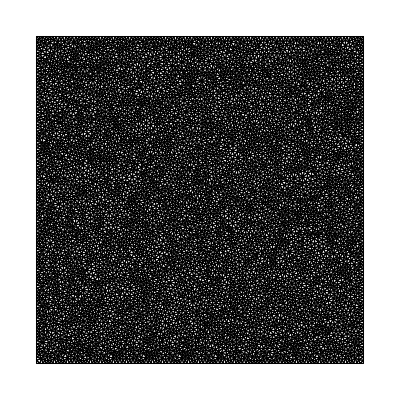

```mathematica
region=Rectangle[{0,0},{1,1}];
Needs["NDSolve`FEM`"];
h=0.0001; 
(*Generate triangular mesh*)
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement",MaxCellMeasure->h];

(*Extract mesh elements and nodes*)
elements=em["MeshElements"][[1,1]];
nodes=em["Coordinates"];

(*Compute triangle centroids for labeling*)
(*centroids=Mean[nodes[[#]]]&/@elements;*)

(*Create text labels for each triangle*)
(*labels=MapThread[Text[Style[#1,12,Blue],#2]&,{Range[Length[elements]],centroids}];*)

(*Show mesh with labeled triangle indices*)
Show[em["Wireframe"](*,Graphics[labels]*)]
```

```mathematica
(*Utils*)
getHatCoefficients[dots_]:=Module[{A,V},(
V=Table[If[j>1,dots[[i,j-1]] ,1],{i,1,3},{j,1,3}];
A=Inverse[V];
A
)]
precomputeHatCoefficients[nodes_,elements_]:=Module[{A,V,dots,nt,i},(
nt=Length[elements];
A=Table[0,nt,3,3];
For[i=1,i≤nt,i++,
dots=nodes[[elements[[i]]]];
A[[i]]=getHatCoefficients[dots]
];
A
)]

(*Finds neighbouring elements in a triangle mesh*)
tri2Tri[nodes_,elements_]:=Module[{nt,np,neighbours, n2e,i,elementsWithNode1, elementsWithNode2, elementsWithNode3, elementsWithEdge1, elementsWithEdge2, elementsWithEdge3 },(
nt=Length[elements];
np=Length[nodes];
neighbours=Table[-1,nt,3];
n2e=GroupBy[Flatten[MapIndexed[#1->First[#2]&,elements,{2}],1],First->Last];
For[i=1,i<=nt,i++,
elementsWithNode1=Lookup[n2e,elements[[i,1]],{}];elementsWithNode2=Lookup[n2e,elements[[i,2]],{}];
elementsWithNode3=Lookup[n2e,elements[[i,3]],{}];
elementsWithEdge1 = DeleteCases[Intersection[elementsWithNode2, elementsWithNode3],i];
If[elementsWithEdge1 ≠ {},
neighbours[[i,1]]=elementsWithEdge1[[1]]
];
elementsWithEdge2=DeleteCases[Intersection[elementsWithNode1,elementsWithNode3],i];
If[elementsWithEdge2 ≠ {},
neighbours[[i,2]]=elementsWithEdge2[[1]]
];
elementsWithEdge3=DeleteCases[Intersection[elementsWithNode1,elementsWithNode2],i];
If[elementsWithEdge3 ≠ {},
neighbours[[i,3]]=elementsWithEdge3[[1]]
];
];
neighbours
)]
```

```mathematica
(*Global variables*)
nt=Length[elements];
np=Length[nodes];
neighbours = tri2Tri[nodes,elements];
hatCoefficients=precomputeHatCoefficients[nodes,elements];force[x_,y_]:=2*Pi^2*Sin[Pi*x]*Sin[Pi*y];
```

```mathematica
nt
```

15936

```mathematica
nodeToElements=GroupBy[Flatten[MapIndexed[#1->First[#2]&,elements,{2}],1],First->Last];//Timing
```

{0.0625,Null}

```mathematica
areaGradHelper[x_,y_]:=Module[{area,b,c},(

{area,b,c}
)]

dG1CellAssembler2D[elements_, nodes_, force_]:=Module[{nt,A,b,coordinates,x,y,dofs,area,c,MK,bK,bb},(
nt = Length[elements];
A=Table[0,3*nt,3*nt];
bb=Table[0,3*nt];
For[i=1,i<=nt,i++,

coordinates=Transpose[nodes[[elements[[i]]]]];
x = coordinates[[1]];
y=coordinates[[2]];
dofs={3*i-2,3*i-1,3*i};
(*TO DO: Move into separate function- perf test first*)
area=0.5*(x[[1]]*y[[2]]+x[[3]]*y[[1]]+x[[2]]*y[[3]]-x[[1]]*y[[3]]-y[[1]]*x[[2]]-y[[2]]*x[[3]]);
b={{y[[2]]-y[[3]],y[[3]]-y[[1]],y[[1]]-y[[2]]}}/2/area;
c={{x[[3]]-x[[2]],x[[1]]-x[[3]],x[[2]]-x[[1]]}}/2/area;

MK=(Transpose[b].b + Transpose[c].c)*area;
bK=1./3*area*force[(x[[1]]+x[[2]]+x[[3]])/3,(y[[1]]+y[[2]]+y[[3]])/3]*{1,1,1};
A[[dofs,dofs]]+=MK;
bb[[dofs]]+=bK;
];
{A,bb}
)]
```

```mathematica
dG1CellAssembler2D[elements,nodes,force];//Timing
```

{108.031,Null}

```mathematica
{34.09375,Null}
```

{34.0938,Null}

```mathematica
dG1EdgeAssembler2D[elements_, nodes_,neighbours_, hatCoefficients_]:=Module[{nt,np,P,S,edge2node,cmat,wvec,dots,area,dx,dy,ds,nx,ny,n,e2n,coordinatesForSimpson,SE,PE,neighbourNodes,q ,i,j,ai,bi,ci,an,bn,cn,ϕi,ϕn,wxlen,jump,avgdn,dofs},(
nt=Length[elements];
np=Length[nodes];
P=Table[0,3*nt,3*nt];
S=Table[0,3*nt,3*nt];
(*i-th element gives us the nodes of the i-th edge*)
edge2node={{2,3},{1,3},{1,2}};
(*coefficients for Simpson integration*)
cmat=0.5*{{2,0},{1,1},{0,2}};
wvec={1.,4.,1.}/6.;
For[i=1,i≤nt,i++,
dots=nodes[[elements[[i]]]];
area=0.5*(dots[[1,1]]*dots[[2,2]]+dots[[1,2]]*dots[[3,1]]+dots[[2,1]]*dots[[3,2]]-dots[[1,1]]*dots[[3,2]]-dots[[1,2]]*dots[[2,1]]-dots[[2,2]]*dots[[3,1]]);
dx={dots[[3,1]]-dots[[2,1]],dots[[1,1]]-dots[[3,1]],dots[[2,1]]-dots[[1,1]]};
dy={dots[[3,2]]-dots[[2,2]],dots[[1,2]]-dots[[3,2]],dots[[2,2]]-dots[[1,2]]};
ds=Sqrt[dx*dx+dy*dy];
nx=-dy/ds;
ny=dx/ds;
For[j=1,j≤3,j++,
(*Kn(K-) and Ki(K+) are neighbours*)
n=neighbours[[i,j]];
If[n>i,Continue[]];
If[n<0,n=i];(*δΩ*)
e2n=edge2node[[j]];(*numbers of nodes on j-th edge*)
coordinatesForSimpson=cmat.dots[[e2n]];
SE=Table[0,6,6];
PE=Table[0,6,6];
neighbourNodes=nodes[[elements[[n]]]];
For[q=1,q≤3,q++,
ai=hatCoefficients[[i]][[1]];
bi=hatCoefficients[[i]][[2]];
ci=hatCoefficients[[i]][[3]];
an=hatCoefficients[[n]][[1]];
bn=hatCoefficients[[n]][[2]];
cn=hatCoefficients[[n]][[3]];
ϕi=ai+bi*coordinatesForSimpson[[q,1]]+ci*coordinatesForSimpson[[q,2]];
ϕn=an+bn*coordinatesForSimpson[[q,1]]+cn*coordinatesForSimpson[[q,2]];
wxlen=wvec[[q]]*ds[[j]];
jump={Join[ϕi,-ϕn]};
avgdn=0.5*{Join[nx[[j]]*bi+ny[[j]]*ci, nx[[j]]*bn+ny[[j]]*cn]};
PE+=Transpose[jump].jump*wxlen;
SE+=Transpose[jump].avgdn*wxlen;
];
dofs={3*i-2,3*i-1,3*i,3*n-2,3*n-1,3*n};
If[n==i,
PE=PE[[{1,2,3},{1,2,3}]];
SE=SE[[{1,2,3},{1,2,3}]];
dofs=dofs[[{1,2,3}]];
];
P[[dofs,dofs]]+=PE;
S[[dofs,dofs]]+=SE;
]
];
{P,S}
)]
```

```mathematica
β=3;
α=-1;

{A,b}=dG1CellAssembler2D[elements,nodes,force];

{P,S}=dG1EdgeAssembler2D[elements,nodes,neighbours,hatCoefficients]
```

{{1},{1}}
 |  |  |  |

```mathematica
U=Inverse[A-S+α*Transpose[S]+β/h*P].b;
```

```mathematica
(*Visualization*)

Y=Table[0,3*nt];
X=Y;
i=elements[[All,1]];
j = elements[[All,2]];
k=elements[[All,3]];
X[[1;; ;;3]]=nodes[[i,1]];
X[[2;; ;;3]]=nodes[[j,1]];
X[[3;; ;;3]]=nodes[[k,1]];
Y[[1;; ;;3]]=nodes[[i,2]];
Y[[2;; ;;3]]=nodes[[j,2]];
Y[[3;; ;;3]]=nodes[[k,2]];
a=Table[Table[{X[[l+3*q]],Y[[l+3*q]],U[[l+3*q]]},{l,1,3}],{q,0,nt-1}];
```

```mathematica
ListPlot3D[a,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*Exact solution*)
Plot3D[Sin[x*Pi]*Sin[Pi*y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
(*Testing*)

hatCoefficients=precomputeHatCoefficients[nodes,elements];
i=2;
dots=nodes[[elements[[i]]]];
edge2node={{2,3},{1,3},{1,2}};
e2n=edge2node[[2]];
cmat=0.5*{{2,0},{1,1},{0,2}};
simpson=cmat.dots[[e2n]];
n=neighbours[[2,2]];
ai=hatCoefficients[[i]][[1]];
bi=hatCoefficients[[i]][[2]];
ci=hatCoefficients[[i]][[3]];
an=hatCoefficients[[n]][[1]];
bn=hatCoefficients[[n]][[2]];
cn=hatCoefficients[[n]][[3]];
```

Part::partw: Part 268 of precomputeHatCoefficients[{{-30.,0.},{-30.,1.},{-30.,2.},{-30.,3.},«43»,{-30.,47.},{-30.,48.},{-30.,49.},«1231»},{{285,74,233},«49»,«2350»}] does not exist.

Part::partw: Part 3 of precomputeHatCoefficients[{{-30.,0.},{-30.,1.},{-30.,2.},{-30.,3.},{-30.,4.},«42»,{-30.,47.},{-30.,48.},{-30.,49.},«1231»},{«1»}]⟦268⟧ does not exist.

```mathematica
nodes[[elements[[n]]]]
```

{{-30.,1.},{-29.,0.},{-28.9021,1.5}}

```mathematica
dots
```

{{-30.,1.},{-30.,0.},{-29.,0.}}

```mathematica
triangle=Triangle[dots];
Plot3D[ai[[2]]+bi[[2]]*x+ci[[2]]*y,{x,y}∈triangle]
```

-Graphics3D-

```mathematica
ai[[3]]+bi[[3]]*x+ci[[3]]*y
```

1.-1. x+4.26326×10^-13 y

```mathematica
hatCoefficients[[i,1]].{1,x,y}/.y->1
```

30.-29. x

```mathematica
getHatCoefficients[dots]
```

{{0.,-29.,30.},{0.,-1.,1.},{1.,-1.,4.26326×10^-13}}

```mathematica
v=Table[If[j>1,dots[[i,j-1]] ,1],{i,1,3},{j,1,3}];
v//MatrixForm
```

(1 | -30. | 1.
1 | -30. | 0.
1 | -29. | 0.)

```mathematica
X=Table[0,10];
X[[3;; ;;3]]={1,2,3};
X
```

{0,0,1,0,0,2,0,0,3,0}

```mathematica
v.ci
```

{0.,0.,1.}

```mathematica
ai+bi*simpson[[3,1]]+ci*simpson[[3,2]]
```

{0.,0.,1.}

```mathematica
elements[[1]]
```

{285,74,233}

{0.,30.,-30.}

{1.,-1.,4.26326×10^-13}

```mathematica
simpson
```

{{-30.,1.},{-29.5,0.5},{-29.,0.}}

```mathematica
a=Table[i+j,{i,1,6},{j,1,6}]
```

{{2,3,4,5,6,7},{3,4,5,6,7,8},{4,5,6,7,8,9},{5,6,7,8,9,10},{6,7,8,9,10,11},{7,8,9,10,11,12}}

```mathematica
a=a[[{1,2,3},{1,2,3}]]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
a
```

{{2,3,4,5,6,7},{3,4,5,6,7,8},{4,5,6,7,8,9},{5,6,7,8,9,10},{6,7,8,9,10,11},{7,8,9,10,11,12}}